```mathematica
basedir="\\\\192.168.1.21\\d\\data\\Cycle 192ter\\exp_3-16-14\\rawdata\\polarizertest\\"
Get[basedir<>"camera_ifg.m"]
minIntens=2000;  (* Schwellenwert zur Unterdrückung schwach beleuchtetet Randbereiche der Kamera *)
(*
loadimage[basedir<>filename]    liefert Array mit den einzelnen Bildern aus der Tiff-Datei.;
fittile[images_,tileDX_,tileDY_,nx_,ny_,minIntensity_,period_]

*)
```

\\192.168.1.21\d\data\Cycle 192ter\exp_3-16-14\rawdata\polarizertest\

```mathematica
LoadDatFile[filename_]:=  ToExpression[Transpose[StringSplit[#,"\t"] & /@ Pick[#,StringMatchQ[#,{"\\**","[*"," *","\t*",""}],False]&@Import[basedir<>filename,"lines"]]]
```

```mathematica
reduceSlotsBy[img_,its_,slotmax_]:=Module[{maxph,maxtim},
maxtim=slotmax/its;
maxph=Length[img]/(slotmax+2);
Flatten[Table[    Join[{img[[1+(ph-1)*(slotmax+2)]]},Table[Total[img[[(ph-1)*(slotmax+2)+1+(tim-1)*its;;(ph-1)*(slotmax+2)+tim*its]],1],{tim,1,maxtim}],{img[[ph*(slotmax+2)]]}]     ,{ph,1,maxph}],1]
]
```

```mathematica
(* alle Bilder eines Multi-Page-Images aufsummieren und auf die Anzahl der nicht leeren Pixel normieren *)
integrateImg[img_]:=(Total[#,2]&/@img)   / Count[Flatten[Total[img]],x_/;x>10]
```

# old magnetic prisms -> 0.0013°

```mathematica
filename = "rockingCam_25Sep1038.tif";
```

```mathematica
img=Reverse[loadimage[basedir<>filename],2]; 
imgreduced=img[[1;;Length[img],4;;48,6;;35]];
```

```mathematica
Grid[{{Dimensions[img],Dimensions[imgreduced]},{ArrayPlot[img[[2]],ColorFunction->GrayLevel],ArrayPlot[imgreduced[[2]],ColorFunction->GrayLevel]}}]
```

{25,50,40} | {25,45,30}
-Graphics- | -Graphics-

```mathematica
phsh=LoadDatFile[ StringReplace[filename,".tif"->".dat"]][[2]] * 1000
(* in milli-degree  *)
```

{146.3,146.4,146.5,146.6,146.71,146.8,146.91,147.01,147.1,147.21,147.3,147.41,147.51,147.6,147.71,147.81,147.91,148.01,148.11,148.2,148.3,148.41,148.51,148.59,148.71}

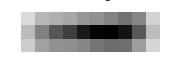
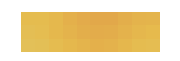
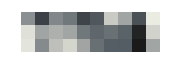
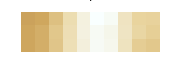

```mathematica
res=fitgridTwoGauss[imgreduced,phsh,3,15,1];
plotresTwoGauss[res]
```

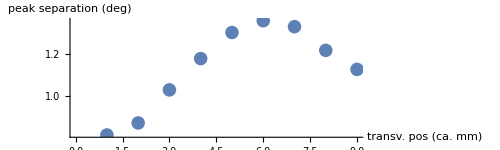

```mathematica
ListPlot[Table[peaksep[res,x,1],{x,0,8}],ImageSize->500,AspectRatio->0.3, AxesLabel->{"transv. pos (ca. mm)","peak separation (deg)" }]
```

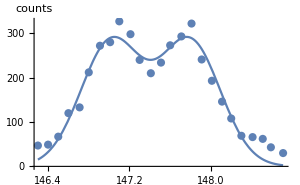
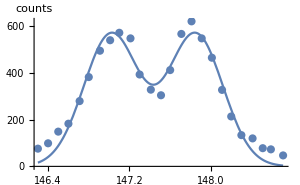
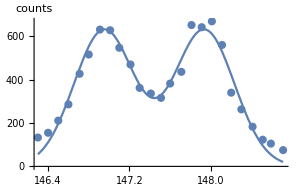
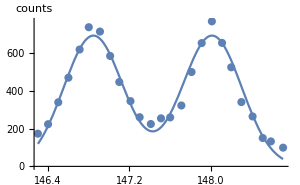
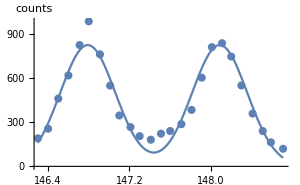
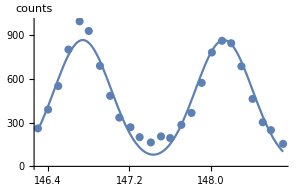
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`b | 281.195 | 11.9094 | 23.6112 | 1.32486×10^-16
CameraIfgPackage`Private`c | 147.019 | 0.0191172 | 7690.38 | 3.26631×10^-69
CameraIfgPackage`Private`d | 0.297836 | 0.0133484 | 22.3124 | 4.1616×10^-16
CameraIfgPackage`Private`sep | 0.77701 | 0.0209155 | 37.15 | 1.21327×10^-20peakheight=281.195
peakpos=147.019
peakwidth=0.297836
peaksep=0.77701
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`b | 568.171 | 19.1234 | 29.7108 | 1.21678×10^-18
CameraIfgPackage`Private`c | 147.021 | 0.0149159 | 9856.68 | 1.78081×10^-71
CameraIfgPackage`Private`d | 0.269822 | 0.00930483 | 28.9981 | 2.0027×10^-18
CameraIfgPackage`Private`sep | 0.827912 | 0.0174769 | 47.3718 | 7.80583×10^-23peakheight=568.171
peakpos=147.021
peakwidth=0.269822
peaksep=0.827912
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`b | 629.641 | 16.9545 | 37.1372 | 1.22195×10^-20
CameraIfgPackage`Private`c | 146.951 | 0.0132888 | 11058.2 | 1.59066×10^-72
CameraIfgPackage`Private`d | 0.295815 | 0.00815394 | 36.2787 | 1.98253×10^-20
CameraIfgPackage`Private`sep | 0.98473 | 0.0162937 | 60.4361 | 4.86114×10^-25peakheight=629.641
peakpos=146.951
peakwidth=0.295815
peaksep=0.98473
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`b | 691.346 | 17.1382 | 40.3395 | 2.20138×10^-21
CameraIfgPackage`Private`c | 146.845 | 0.012149 | 12087. | 2.45627×10^-73
CameraIfgPackage`Private`d | 0.290827 | 0.00759951 | 38.2691 | 6.56214×10^-21
CameraIfgPackage`Private`sep | 1.1663 | 0.0161556 | 72.1916 | 1.1836×10^-26peakheight=691.346
peakpos=146.845
peakwidth=0.290827
peaksep=1.1663
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`b | 827.004 | 26.1362 | 31.642 | 3.33326×10^-19
CameraIfgPackage`Private`c | 146.79 | 0.0143349 | 10240. | 7.99154×10^-72
CameraIfgPackage`Private`d | 0.270945 | 0.00960047 | 28.2221 | 3.49206×10^-18
CameraIfgPackage`Private`sep | 1.29699 | 0.0198849 | 65.225 | 9.88091×10^-26peakheight=827.004
peakpos=146.79
peakwidth=0.270945
peaksep=1.29699
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`b | 864.806 | 24.824 | 34.8374 | 4.58317×10^-20
CameraIfgPackage`Private`c | 146.741 | 0.0135842 | 10802.3 | 2.60072×10^-72
CameraIfgPackage`Private`d | 0.280051 | 0.00931141 | 30.0761 | 9.46655×10^-19
CameraIfgPackage`Private`sep | 1.38762 | 0.018797 | 73.8215 | 7.41909×10^-27peakheight=864.806
peakpos=146.741
peakwidth=0.280051
peaksep=1.38762

```mathematica
Column[Table[showtileresTwoGauss[res,x,2],{x,0,5}]]
```

# new polarizer with alternating oriented magnets -> no splitting

```mathematica
(* cf. R_28Sep1426.dat, R_28Sep1430.dat *)
```

# 1st change: only magnets in one direction -> 0.0011°

```mathematica
(* Öffnung schaut nach rechts *)
```

```mathematica
filename = "rockingCam_28Sep1526.tif";
```

```mathematica
img=Reverse[loadimage[basedir<>filename],2]; 
imgreduced=img[[1;;Length[img],6;;50,6;;35]];
```

```mathematica
Grid[{{Dimensions[img],Dimensions[imgreduced]},{ArrayPlot[img[[2]],ColorFunction->GrayLevel],ArrayPlot[imgreduced[[2]],ColorFunction->GrayLevel]}}]
```

{25,50,40} | {25,45,30}
-Graphics- | -Graphics-

```mathematica
phsh=1000*LoadDatFile[ StringReplace[filename,".tif"->".dat"]][[2]]
```

{146.6,146.71,146.8,146.9,147.,147.11,147.2,147.3,147.41,147.5,147.6,147.7,147.8,147.91,148.01,148.11,148.2,148.3,148.41,148.5,148.61,148.71,148.81,148.91,149.}

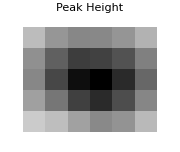
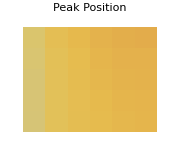
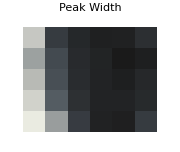
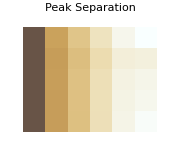

```mathematica
res=fitgridTwoGauss[imgreduced,phsh,5,9,1];
plotresTwoGauss[res]
```

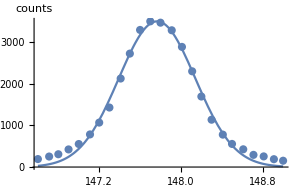
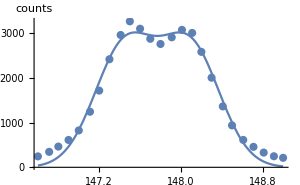
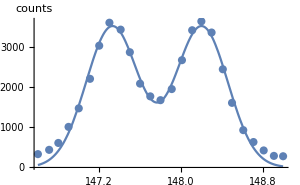
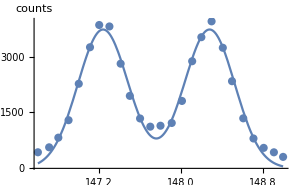
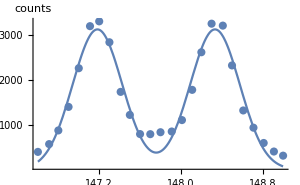
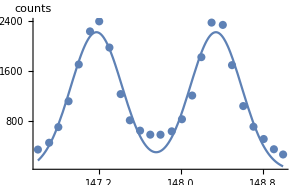
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`b | 1752.7 | 31.2354 | 56.1127 | 2.28919×10^-24
CameraIfgPackage`Private`c | 147.766 | 0.941541 | 156.941 | 1.01108×10^-33
CameraIfgPackage`Private`d | 0.375924 | 0.00773039 | 48.6294 | 4.52411×10^-23
CameraIfgPackage`Private`sep | -0.0000243047 | 1.88313 | -0.0000129066 | 0.99999peakheight=1752.7
peakpos=147.766
peakwidth=0.375924
peaksep=0.0000243047
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`b | 2688.6 | 91.5643 | 29.363 | 1.54952×10^-18
CameraIfgPackage`Private`c | 147.447 | 0.0125408 | 11757.4 | 4.38969×10^-73
CameraIfgPackage`Private`d | 0.291924 | 0.0108776 | 26.8373 | 9.77454×10^-18
CameraIfgPackage`Private`sep | 0.642149 | 0.0141518 | 45.3759 | 1.91153×10^-22peakheight=2688.6
peakpos=147.447
peakwidth=0.291924
peaksep=0.642149
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`b | 3520.47 | 69.0001 | 51.0212 | 1.66399×10^-23
CameraIfgPackage`Private`c | 147.328 | 0.00831078 | 17727.3 | 7.89694×10^-77
CameraIfgPackage`Private`d | 0.255391 | 0.00512498 | 49.8325 | 2.71933×10^-23
CameraIfgPackage`Private`sep | 0.875408 | 0.0104359 | 83.8841 | 5.11317×10^-28peakheight=3520.47
peakpos=147.328
peakwidth=0.255391
peaksep=0.875408
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`b | 3725.2 | 80.4673 | 46.2946 | 1.25976×10^-22
CameraIfgPackage`Private`c | 147.238 | 0.0088722 | 16595.4 | 3.15658×10^-76
CameraIfgPackage`Private`d | 0.246954 | 0.00562842 | 43.8762 | 3.84444×10^-22
CameraIfgPackage`Private`sep | 1.04275 | 0.0120399 | 86.608 | 2.61851×10^-28peakheight=3725.2
peakpos=147.238
peakwidth=0.246954
peaksep=1.04275
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`b | 3117.6 | 92.6389 | 33.6533 | 9.35943×10^-20
CameraIfgPackage`Private`c | 147.183 | 0.0119596 | 12306.7 | 1.68261×10^-73
CameraIfgPackage`Private`d | 0.243188 | 0.00789409 | 30.8063 | 5.78195×10^-19
CameraIfgPackage`Private`sep | 1.15079 | 0.0165891 | 69.3704 | 2.7247×10^-26peakheight=3117.6
peakpos=147.183
peakwidth=0.243188
peaksep=1.15079
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`b | 2223.74 | 68.9243 | 32.2635 | 2.23306×10^-19
CameraIfgPackage`Private`c | 147.173 | 0.0129154 | 11395.1 | 8.46961×10^-73
CameraIfgPackage`Private`d | 0.251793 | 0.00848028 | 29.6916 | 1.233×10^-18
CameraIfgPackage`Private`sep | 1.16927 | 0.0178666 | 65.4443 | 9.21128×10^-26peakheight=2223.74
peakpos=147.173
peakwidth=0.251793
peaksep=1.16927

```mathematica
Column[Table[showtileresTwoGauss[res,x,2],{x,0,5}]]
```

# 2nd change: closing return flux (using 5 magnets) -> 0.0013°

```mathematica
(* Öffnung schaut nach links *)
```

```mathematica
filename = "rockingCam_29Sep1403.tif";
```

```mathematica
img=Reverse[loadimage[basedir<>filename],2]; 
imgreduced=img[[1;;Length[img],6;;50,6;;35]];
```

```mathematica
Grid[{{Dimensions[img],Dimensions[imgreduced]},{ArrayPlot[img[[2]],ColorFunction->GrayLevel],ArrayPlot[imgreduced[[2]],ColorFunction->GrayLevel]}}]
```

{25,50,40} | {25,45,30}
-Graphics- | -Graphics-

```mathematica
phsh=1000*LoadDatFile[ StringReplace[filename,".tif"->".dat"]][[2]]
```

{146.6,146.71,146.8,146.91,147.,147.11,147.21,147.3,147.41,147.5,147.6,147.7,147.8,147.91,148.01,148.11,148.2,148.31,148.41,148.51,148.6,148.7,148.81,148.91,149.}

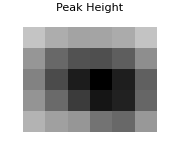
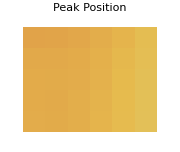
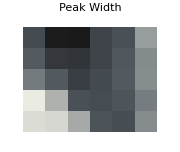
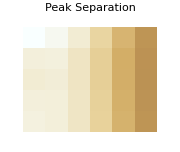

```mathematica
res=fitgridTwoGauss[imgreduced,phsh,5,9,1];
plotresTwoGauss[res]
```

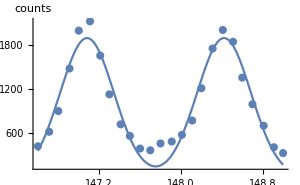
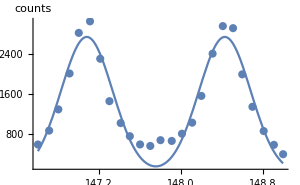
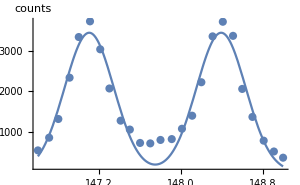
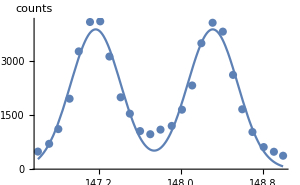
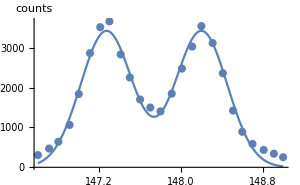
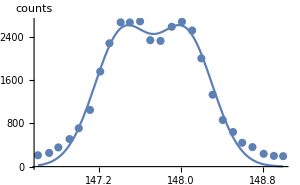
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`b | 1891.89 | 61.8875 | 30.5699 | 6.77414×10^-19
CameraIfgPackage`Private`c | 147.081 | 0.0142486 | 10322.5 | 6.75303×10^-72
CameraIfgPackage`Private`d | 0.263886 | 0.0098782 | 26.714 | 1.07385×10^-17
CameraIfgPackage`Private`sep | 1.34099 | 0.0199381 | 67.2576 | 5.20228×10^-26peakheight=1891.89
peakpos=147.081
peakwidth=0.263886
peaksep=1.34099
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`b | 2736.92 | 106.343 | 25.7366 | 2.29738×10^-17
CameraIfgPackage`Private`c | 147.078 | 0.0161541 | 9104.69 | 9.42745×10^-71
CameraIfgPackage`Private`d | 0.253126 | 0.0113305 | 22.3402 | 4.05834×10^-16
CameraIfgPackage`Private`sep | 1.351 | 0.0227201 | 59.4625 | 6.82375×10^-25peakheight=2736.92
peakpos=147.078
peakwidth=0.253126
peaksep=1.351
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`b | 3442.46 | 124.924 | 27.5564 | 5.69226×10^-18
CameraIfgPackage`Private`c | 147.102 | 0.0142672 | 10310.5 | 6.91944×10^-72
CameraIfgPackage`Private`d | 0.240873 | 0.00997504 | 24.1475 | 8.40041×10^-17
CameraIfgPackage`Private`sep | 1.29141 | 0.0200545 | 64.3949 | 1.29138×10^-25peakheight=3442.46
peakpos=147.102
peakwidth=0.240873
peaksep=1.29141
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`b | 3873.07 | 116.991 | 33.1057 | 1.31284×10^-19
CameraIfgPackage`Private`c | 147.165 | 0.0122192 | 12043.8 | 2.64814×10^-73
CameraIfgPackage`Private`d | 0.246025 | 0.00809878 | 30.3781 | 7.71001×10^-19
CameraIfgPackage`Private`sep | 1.14612 | 0.0168719 | 67.9304 | 4.22488×10^-26peakheight=3873.07
peakpos=147.165
peakwidth=0.246025
peaksep=1.14612
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`b | 3421.8 | 71.0035 | 48.192 | 5.46041×10^-23
CameraIfgPackage`Private`c | 147.271 | 0.00876282 | 16806.4 | 2.42114×10^-76
CameraIfgPackage`Private`d | 0.253087 | 0.00535524 | 47.2597 | 8.20033×10^-23
CameraIfgPackage`Private`sep | 0.929484 | 0.0112847 | 82.3668 | 7.49362×10^-28peakheight=3421.8
peakpos=147.271
peakwidth=0.253087
peaksep=0.929484
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`b | 2409.24 | 81.9304 | 29.4059 | 1.50374×10^-18
CameraIfgPackage`Private`c | 147.42 | 0.0124313 | 11858.7 | 3.66597×10^-73
CameraIfgPackage`Private`d | 0.269191 | 0.00991662 | 27.1454 | 7.74022×10^-18
CameraIfgPackage`Private`sep | 0.625876 | 0.0137238 | 45.6053 | 1.7212×10^-22peakheight=2409.24
peakpos=147.42
peakwidth=0.269191
peaksep=0.625876

```mathematica
Column[Table[showtileresTwoGauss[res,x,2],{x,0,5}]]
```

# Test of image orientation -> ok

```mathematica
testimg1=Reverse[loadimage[basedir<>"orientation.tif"],2];
testimg2=Reverse[loadimage[basedir<>"orientation+Cd_on_left.tif"],2];
```

```mathematica
Row[{ArrayPlot[testimg1[[1]],ColorFunction->GrayLevel] ,ArrayPlot[testimg2[[1]],ColorFunction->GrayLevel] }]
```

-Graphics--Graphics-

# 3rd change: shift 3mm to right, Cd on left, -> 0.0014°

```mathematica
(* Öffnung schaut nach links *)
(* Schnelldurchgang -> Bildspalten vertikal komplett aufsummieren *)
```

```mathematica
filename = "rockingCam_29Sep2018.tif";
```

```mathematica
img=Reverse[loadimage[basedir<>filename],2]; 
imgreduced=img[[1;;Length[img],6;;50,6;;35]];
```

```mathematica
Grid[{{Dimensions[img],Dimensions[imgreduced]},{ArrayPlot[img[[2]],ColorFunction->GrayLevel],ArrayPlot[imgreduced[[2]],ColorFunction->GrayLevel]}}]
```

{25,50,40} | {25,45,30}
-Graphics- | -Graphics-

```mathematica
phsh=1000*LoadDatFile[ StringReplace[filename,".tif"->".dat"]][[2]]
```

{146.6,146.71,146.81,146.91,147.01,147.11,147.21,147.3,147.4,147.51,147.61,147.71,147.8,147.91,147.99,148.1,148.22,148.3,148.41,148.5,148.61,148.71,148.8,148.91,149.}

```mathematica
res=fitgridTwoGauss[imgreduced,phsh,5,45,1];
plotresTwoGauss[res]
```

-Graphics--Graphics--Graphics--Graphics-

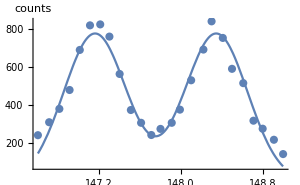
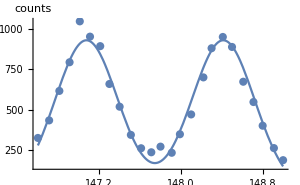
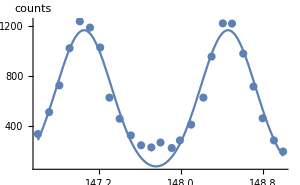
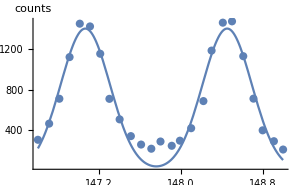
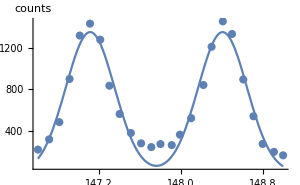
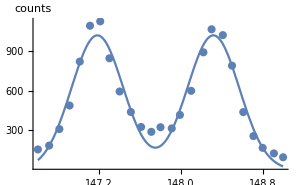
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`b | 774.88 | 20.3699 | 38.0404 | 7.42968×10^-21
CameraIfgPackage`Private`c | 147.159 | 0.0137438 | 10707.3 | 3.13117×10^-72
CameraIfgPackage`Private`d | 0.305897 | 0.00845185 | 36.1929 | 2.0821×10^-20
CameraIfgPackage`Private`sep | 1.18654 | 0.0180022 | 65.9109 | 7.94019×10^-26peakheight=774.88
peakpos=147.159
peakwidth=0.305897
peaksep=1.18654
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`b | 931.322 | 20.5022 | 45.4255 | 1.86851×10^-22
CameraIfgPackage`Private`c | 147.075 | 0.0116306 | 12645.5 | 9.51213×10^-74
CameraIfgPackage`Private`d | 0.305643 | 0.00756326 | 40.4115 | 2.12142×10^-21
CameraIfgPackage`Private`sep | 1.3393 | 0.0157201 | 85.197 | 3.69362×10^-28peakheight=931.322
peakpos=147.075
peakwidth=0.305643
peaksep=1.3393
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`b | 1167.11 | 34.5755 | 33.7553 | 8.79251×10^-20
CameraIfgPackage`Private`c | 147.052 | 0.01341 | 10965.8 | 1.89716×10^-72
CameraIfgPackage`Private`d | 0.27041 | 0.00944126 | 28.6413 | 2.58142×10^-18
CameraIfgPackage`Private`sep | 1.40939 | 0.0186925 | 75.399 | 4.7666×10^-27peakheight=1167.11
peakpos=147.052
peakwidth=0.27041
peaksep=1.40939
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`b | 1401.68 | 48.339 | 28.9968 | 2.00448×10^-18
CameraIfgPackage`Private`c | 147.064 | 0.0137003 | 10734.4 | 2.96923×10^-72
CameraIfgPackage`Private`d | 0.241653 | 0.009796 | 24.6685 | 5.44474×10^-17
CameraIfgPackage`Private`sep | 1.38861 | 0.0193105 | 71.9099 | 1.28446×10^-26peakheight=1401.68
peakpos=147.064
peakwidth=0.241653
peaksep=1.38861
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`b | 1348.76 | 44.8676 | 30.061 | 9.56521×10^-19
CameraIfgPackage`Private`c | 147.111 | 0.0131546 | 11183.3 | 1.25605×10^-72
CameraIfgPackage`Private`d | 0.238614 | 0.00916495 | 26.0355 | 1.81548×10^-17
CameraIfgPackage`Private`sep | 1.2965 | 0.018565 | 69.8358 | 2.36911×10^-26peakheight=1348.76
peakpos=147.111
peakwidth=0.238614
peaksep=1.2965
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`b | 1018.03 | 32.2399 | 31.5766 | 3.47835×10^-19
CameraIfgPackage`Private`c | 147.182 | 0.0136267 | 10801. | 2.60744×10^-72
CameraIfgPackage`Private`d | 0.254645 | 0.00866192 | 29.3982 | 1.51186×10^-18
CameraIfgPackage`Private`sep | 1.13556 | 0.0187215 | 60.6553 | 4.50714×10^-25peakheight=1018.03
peakpos=147.182
peakwidth=0.254645
peaksep=1.13556

```mathematica
Column[Table[showtileresTwoGauss[res,x,0],{x,0,5}]]
```

# 4th change: iron bars removed on top and bottom -> no change

```mathematica
(* Öffnung schaut nach links *)
```

```mathematica
filename = "rockingCam_29Sep2059.tif";
```

```mathematica
img=Reverse[loadimage[basedir<>filename],2]; 
imgreduced=img[[1;;Length[img],6;;50,6;;34]];
```

```mathematica
Grid[{{Dimensions[img],Dimensions[imgreduced]},{ArrayPlot[img[[2]],ColorFunction->GrayLevel],ArrayPlot[imgreduced[[2]],ColorFunction->GrayLevel]}}]
```

{25,50,40} | {25,45,29}
-Graphics- | -Graphics-

```mathematica
phsh=1000*LoadDatFile[ StringReplace[filename,".tif"->".dat"]][[2]]
```

{146.61,146.71,146.8,146.9,147.01,147.11,147.21,147.3,147.41,147.51,147.61,147.71,147.81,147.9,148.,148.11,148.21,148.3,148.41,148.5,148.6,148.69,148.8,148.91,149.}

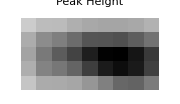
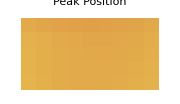
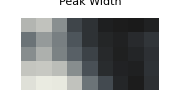
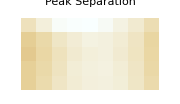

```mathematica
res=fitgridTwoGauss[imgreduced,phsh,3,9,1];
plotresTwoGauss[res]
```

```mathematica
peaksepTable[res]
```

{{1.30553,1.40008,1.48948,1.50725,1.51213,1.48031,1.42314,1.36579,1.27651},{1.16801,1.24597,1.3366,1.38204,1.42056,1.41019,1.38053,1.32511,1.22332},{1.13825,1.23146,1.30778,1.36712,1.39884,1.40947,1.36904,1.32081,1.22983},{1.18164,1.2457,1.31758,1.38506,1.40807,1.41535,1.3865,1.33109,1.23968},{1.18298,1.2568,1.33315,1.38015,1.40328,1.41146,1.39098,1.33473,1.25317}}

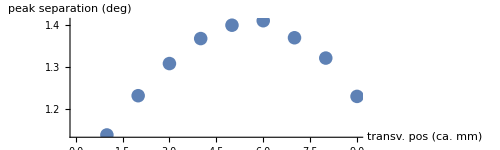

```mathematica
ListPlot[Table[peaksep[res,x,2],{x,0,8}],ImageSize->500,AspectRatio->0.3, AxesLabel->{"transv. pos (ca. mm)","peak separation (deg)" }]
```

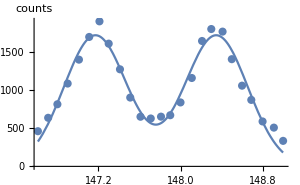
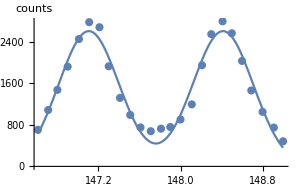
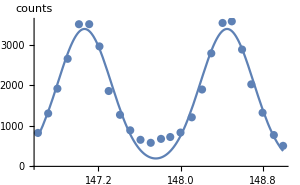
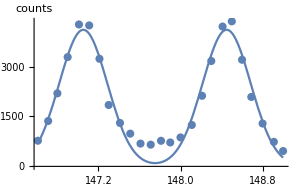
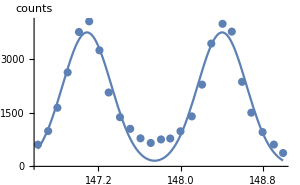
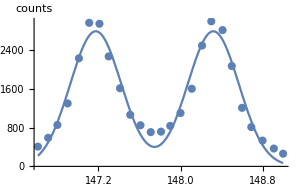
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`b | 1721.27 | 41.3976 | 41.5789 | 1.17478×10^-21
CameraIfgPackage`Private`c | 147.171 | 0.0125334 | 11742.2 | 4.51029×10^-73
CameraIfgPackage`Private`d | 0.307265 | 0.00774664 | 39.6643 | 3.12407×10^-21
CameraIfgPackage`Private`sep | 1.17786 | 0.0163812 | 71.903 | 1.28706×10^-26peakheight=1721.27
peakpos=147.171
peakwidth=0.307265
peaksep=1.17786
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`b | 2603.33 | 63.6801 | 40.8814 | 1.66904×10^-21
CameraIfgPackage`Private`c | 147.106 | 0.0121681 | 12089.5 | 2.44575×10^-73
CameraIfgPackage`Private`d | 0.294284 | 0.0079953 | 36.8071 | 1.46998×10^-20
CameraIfgPackage`Private`sep | 1.30809 | 0.0166579 | 78.5267 | 2.03597×10^-27peakheight=2603.33
peakpos=147.106
peakwidth=0.294284
peaksep=1.30809
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`b | 3392.92 | 93.6384 | 36.2342 | 2.03352×10^-20
CameraIfgPackage`Private`c | 147.064 | 0.0119033 | 12355. | 1.5499×10^-73
CameraIfgPackage`Private`d | 0.260892 | 0.00842442 | 30.9686 | 5.18971×10^-19
CameraIfgPackage`Private`sep | 1.38971 | 0.016727 | 83.0819 | 6.25292×10^-28peakheight=3392.92
peakpos=147.064
peakwidth=0.260892
peaksep=1.38971
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`b | 4105.6 | 137.688 | 29.8181 | 1.12994×10^-18
CameraIfgPackage`Private`c | 147.052 | 0.0128548 | 11439.5 | 7.80641×10^-73
CameraIfgPackage`Private`d | 0.234942 | 0.00925128 | 25.3957 | 3.0147×10^-17
CameraIfgPackage`Private`sep | 1.39727 | 0.0181581 | 76.9503 | 3.11248×10^-27peakheight=4105.6
peakpos=147.052
peakwidth=0.234942
peaksep=1.39727
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`b | 3740.69 | 132.644 | 28.201 | 3.54586×10^-18
CameraIfgPackage`Private`c | 147.088 | 0.0138428 | 10625.6 | 3.67723×10^-72
CameraIfgPackage`Private`d | 0.237237 | 0.00973177 | 24.3776 | 6.92914×10^-17
CameraIfgPackage`Private`sep | 1.31724 | 0.0194507 | 67.7219 | 4.50535×10^-26peakheight=3740.69
peakpos=147.088
peakwidth=0.237237
peaksep=1.31724
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`b | 2781.27 | 83.3132 | 33.3833 | 1.10512×10^-19
CameraIfgPackage`Private`c | 147.174 | 0.0126128 | 11668.6 | 5.14681×10^-73
CameraIfgPackage`Private`d | 0.249792 | 0.00810593 | 30.816 | 5.74469×10^-19
CameraIfgPackage`Private`sep | 1.14589 | 0.0172929 | 66.2635 | 7.10218×10^-26peakheight=2781.27
peakpos=147.174
peakwidth=0.249792
peaksep=1.14589

```mathematica
Column[Table[showtileresTwoGauss[res,x,2],{x,0,5}]]
```

```mathematica
(* Öffnung schaut nach links *)
```

```mathematica
filename = "rockingCam_30Sep0120.tif";
```

```mathematica
img=Reverse[loadimage[basedir<>filename],2]; 
imgreduced=img[[1;;Length[img],6;;50,6;;35]];
```

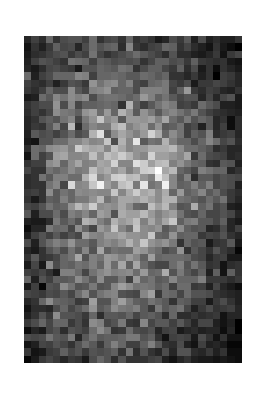
{25,50,40} | {25,45,30}
-Graphics- | -Graphics-

```mathematica
Grid[{{Dimensions[img],Dimensions[imgreduced]},{ArrayPlot[img[[2]],ColorFunction->GrayLevel],ArrayPlot[imgreduced[[2]],ColorFunction->GrayLevel]}}]
```

```mathematica
phsh=1000*LoadDatFile[ StringReplace[filename,".tif"->".dat"]][[2]]
```

{146.6,146.71,146.81,146.9,147.,147.11,147.2,147.3,147.4,147.5,147.6,147.7,147.8,147.9,148.,148.11,148.2,148.3,148.4,148.52,148.6,148.7,148.81,148.9,149.}

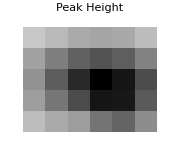
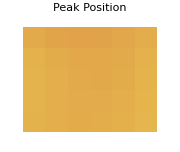
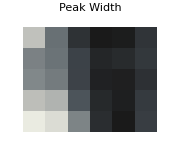
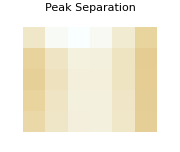

```mathematica
res=fitgridTwoGauss[imgreduced,phsh,5,9,1];
plotresTwoGauss[res]
```

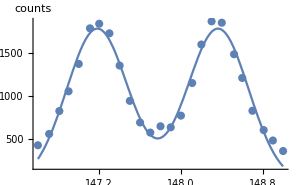
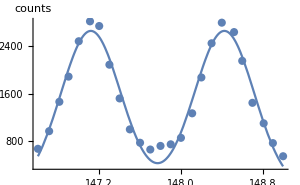
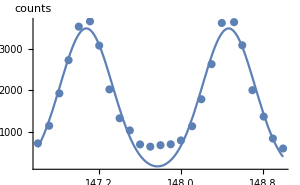
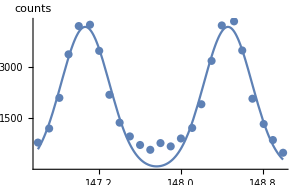
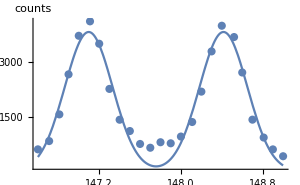
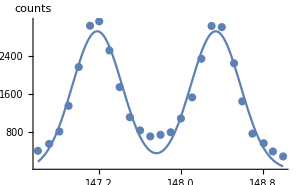
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`b | 1783.8 | 38.5771 | 46.2398 | 1.29121×10^-22
CameraIfgPackage`Private`c | 147.181 | 0.0107962 | 13632.7 | 1.96236×10^-74
CameraIfgPackage`Private`d | 0.299528 | 0.00679398 | 44.0873 | 3.4794×10^-22
CameraIfgPackage`Private`sep | 1.1815 | 0.014287 | 82.6975 | 6.89058×10^-28peakheight=1783.8
peakpos=147.181
peakwidth=0.299528
peaksep=1.1815
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`b | 2644.24 | 58.0638 | 45.5403 | 1.77303×10^-22
CameraIfgPackage`Private`c | 147.118 | 0.010696 | 13754.5 | 1.6278×10^-74
CameraIfgPackage`Private`d | 0.292876 | 0.00712136 | 41.1264 | 1.47437×10^-21
CameraIfgPackage`Private`sep | 1.30706 | 0.0146495 | 89.2221 | 1.40459×10^-28peakheight=2644.24
peakpos=147.118
peakwidth=0.292876
peaksep=1.30706
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`b | 3484.79 | 104.12 | 33.4689 | 1.04829×10^-19
CameraIfgPackage`Private`c | 147.074 | 0.0124712 | 11793. | 4.11932×10^-73
CameraIfgPackage`Private`d | 0.256557 | 0.00891114 | 28.7906 | 2.32045×10^-18
CameraIfgPackage`Private`sep | 1.39337 | 0.0175249 | 79.5079 | 1.56993×10^-27peakheight=3484.79
peakpos=147.074
peakwidth=0.256557
peaksep=1.39337
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`b | 4155.45 | 130.513 | 31.8392 | 2.93304×10^-19
CameraIfgPackage`Private`c | 147.063 | 0.0118951 | 12363.3 | 1.52798×10^-73
CameraIfgPackage`Private`d | 0.235498 | 0.00860126 | 27.3794 | 6.49428×10^-18
CameraIfgPackage`Private`sep | 1.39671 | 0.0167799 | 83.2371 | 6.01328×10^-28peakheight=4155.45
peakpos=147.063
peakwidth=0.235498
peaksep=1.39671
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`b | 3811.09 | 132.407 | 28.7831 | 2.3329×10^-18
CameraIfgPackage`Private`c | 147.097 | 0.013092 | 11235.7 | 1.13861×10^-72
CameraIfgPackage`Private`d | 0.234183 | 0.00933431 | 25.0884 | 3.8626×10^-17
CameraIfgPackage`Private`sep | 1.31918 | 0.0184108 | 71.6528 | 1.38441×10^-26peakheight=3811.09
peakpos=147.097
peakwidth=0.234183
peaksep=1.31918
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`b | 2910.74 | 86.6407 | 33.5956 | 9.69679×10^-20
CameraIfgPackage`Private`c | 147.181 | 0.0120076 | 12257.3 | 1.83106×10^-73
CameraIfgPackage`Private`d | 0.244802 | 0.00794619 | 30.8074 | 5.77746×10^-19
CameraIfgPackage`Private`sep | 1.15936 | 0.0166346 | 69.6957 | 2.47074×10^-26peakheight=2910.74
peakpos=147.181
peakwidth=0.244802
peaksep=1.15936

```mathematica
Column[Table[showtileresTwoGauss[res,x,2],{x,0,5}]]
```

# tempered silicon test

```mathematica
(* Öffnung schaut nach links *)
```

```mathematica
filename = "rockingCam_30Sep1039.tif";
```

```mathematica
img=Reverse[loadimage[basedir<>"..\\temperedSiTest\\"<>filename],2]; 
imgreduced=img[[1;;Length[img],12;;59,11;;58]];
```

```mathematica
Grid[{{Dimensions[img],Dimensions[imgreduced]},{ArrayPlot[img[[2]],ColorFunction->GrayLevel],ArrayPlot[imgreduced[[2]],ColorFunction->GrayLevel]}}]
```

{36,64,64} | {36,48,48}
-Graphics- | -Graphics-

```mathematica
phsh=1000*LoadDatFile[ StringReplace["..\\temperedSiTest\\"<>filename,".tif"->".dat"]][[2]]
```

{1327.2,1327.41,1327.6,1327.8,1328.02,1328.21,1328.41,1328.61,1328.79,1329.01,1329.2,1329.41,1329.61,1329.81,1330.01,1330.2,1330.41,1330.6,1330.8,1330.99,1331.2,1331.43,1331.61,1331.82,1331.99,1332.2,1332.39,1332.6,1332.8,1333.,1333.21,1333.4,1333.6,1333.81,1334.01,1334.21}

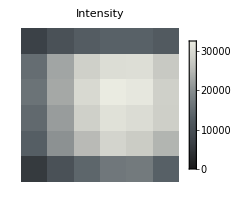
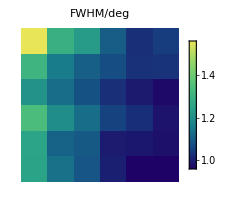
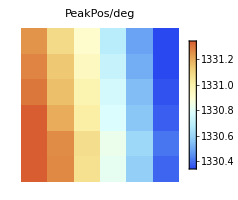

```mathematica
res=fitgridGauss[imgreduced,phsh,8,8,1,0.5];
plotresGauss[res,200,0.3,0.5]
```

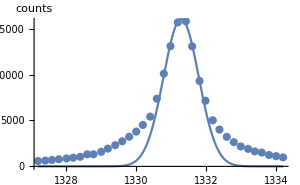
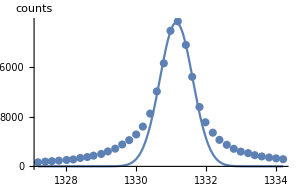
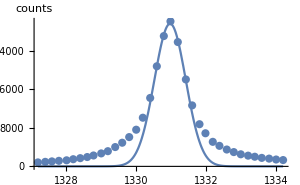
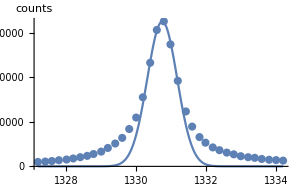
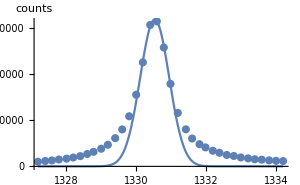
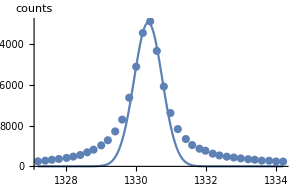
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`b | 16061.4 | 194.059 | 82.7655 | 3.88772×10^-6
CameraIfgPackage`Private`c | 1331.3 | 0.00752146 | 177000. | 3.97699×10^-16
CameraIfgPackage`Private`d | 0.503708 | 0.0124292 | 40.5262 | 0.0000330608peakheight=16061.4
peakpos=1331.3
width(sigma)=0.503708
FWHM=1.21003
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`b | 23086.5 | 414.412 | 55.709 | 0.0000127406
CameraIfgPackage`Private`c | 1331.16 | 0.01032 | 128988. | 1.0276×10^-15
CameraIfgPackage`Private`d | 0.470508 | 0.01582 | 29.7413 | 0.0000834882peakheight=23086.5
peakpos=1331.16
width(sigma)=0.470508
FWHM=1.13028
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`b | 29659.4 | 381.881 | 77.6666 | 0.000165739
CameraIfgPackage`Private`c | 1330.98 | 0.007879 | 168927. | 3.5043×10^-11
CameraIfgPackage`Private`d | 0.448661 | 0.0131203 | 34.1959 | 0.000854072peakheight=29659.4
peakpos=1330.98
width(sigma)=0.448661
FWHM=1.07779
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`b | 32503.1 | 379.439 | 85.661 | 0.000136253
CameraIfgPackage`Private`c | 1330.76 | 0.00680386 | 195588. | 2.61405×10^-11
CameraIfgPackage`Private`d | 0.426948 | 0.0113123 | 37.7419 | 0.000701285peakheight=32503.1
peakpos=1330.76
width(sigma)=0.426948
FWHM=1.02563
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`b | 31947.3 | 314.177 | 101.686 | 0.000096698
CameraIfgPackage`Private`c | 1330.54 | 0.00557186 | 238796. | 1.75366×10^-11
CameraIfgPackage`Private`d | 0.414145 | 0.00881279 | 46.9936 | 0.00045251peakheight=31947.3
peakpos=1330.54
width(sigma)=0.414145
FWHM=0.994877
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`b | 28242.4 | 527.804 | 53.5094 | 0.00034907
CameraIfgPackage`Private`c | 1330.35 | 0.00977374 | 136115. | 5.39744×10^-11
CameraIfgPackage`Private`d | 0.402893 | 0.0155474 | 25.9139 | 0.00148582peakheight=28242.4
peakpos=1330.35
width(sigma)=0.402893
FWHM=0.967847

```mathematica
Column[Table[showtileresGauss[res,x,2],{x,0,5}]]
```